```mathematica
trainlls={{-4.10533389,-4.02407462,-3.95812022,-3.90443111,-3.86099218,-3.82532771,-3.79608793,-3.77207505,-3.75231147,-3.73571205},{-4.29852937,-4.16951254,-4.06741535,-3.98686472,-3.92299039,-3.87206111,-3.83123112,-3.79824021,-3.7713563,-3.74906935},{-4.62063409,-4.42331313,-4.26601208,-4.14042149,-4.0400228,-3.9592978,-3.89452929,-3.84216468,-3.7996268,-3.76477963},{-5.32971132,-4.99570845,-4.72774879,-4.51129239,-4.33855,-4.19831876,-4.08442487,-3.99177357,-3.91575996,-3.85298163},{-5.5339999,-5.14871145,-4.84040481,-4.59360795,-4.3947661,-4.23676797,-4.10910344,-4.00652216,-3.92402068,-3.85743851},{-6.07384437,-5.60100697,-5.219061,-4.91311601,-4.66564588,-4.46554849,-4.3029043,-4.16984538,-4.06110402,-3.9714046},{-6.43056053,-5.87907712,-5.43801912,-5.08195889,-4.79470026,-4.56044375,-4.37214306,-4.21838124,-4.0928253,-3.98976209},{-7.14352932,-6.49207609,-5.96329911,-5.53166749,-5.1791844,-4.8888645,-4.64909664,-4.45102011,-4.28676623,-4.14980925},{-7.32005317,-6.61324445,-6.04054553,-5.57724425,-5.19877073,-4.88884681,-4.63621586,-4.42782705,-4.25512076,-4.11181345},{-7.64459643,-6.86261631,-6.23364822,-5.72576041,-5.31425337,-4.97860724,-4.70457847,-4.48024834,-4.29537027,-4.14255643}} (*trainLLs*);
```

```mathematica
testlls={{-4.0359547,-3.96654617,-3.90994744,-3.86368779,-3.8259123,-3.79458028,-3.76874477,-3.74726815,-3.72953153,-3.71441615},{-4.24626399,-4.13265246,-4.04255689,-3.97068118,-3.9137229,-3.86771108,-3.83080852,-3.8009209,-3.77639944,-3.75618057},{-4.58484113,-4.4153167,-4.27872785,-4.16823564,-4.0788503,-4.00594871,-3.94646651,-3.89797111,-3.85794479,-3.82525838},{-5.29206877,-5.00437973,-4.77030798,-4.57850937,-4.42314738,-4.29523864,-4.18934429,-4.10230243,-4.02975772,-3.96942343},{-5.48016152,-5.14950506,-4.88131623,-4.66374684,-4.48619446,-4.34286864,-4.22544263,-4.13008509,-4.05260071,-3.98957713},{-6.14553807,-5.72650886,-5.38315032,-5.10388249,-4.87420288,-4.68570138,-4.53014742,-4.40069542,-4.29342982,-4.20412162},{-6.51063124,-6.02517405,-5.62954333,-5.30380836,-5.03516911,-4.81184342,-4.62906984,-4.47703909,-4.35081548,-4.24536357},{-7.23349453,-6.67108453,-6.20628245,-5.81874752,-5.49611104,-5.22470358,-4.99603124,-4.80404111,-4.64210398,-4.50512188},{-7.45458181,-6.84482243,-6.33909318,-5.92099675,-5.57164207,-5.27934498,-5.03586249,-4.83080985,-4.6575543,-4.51131354},{-7.72486097,-7.06674319,-6.52522504,-6.07780668,-5.70648949,-5.39677942,-5.138622,-4.92247838,-4.74123565,-4.58885067}} (*testLLs*);
```

```mathematica
trainmllbs={{-104.19178541,-103.99777047,-103.82140691,-103.65907896,-103.50935419,-103.36842044,-103.23511099,-103.10807423,-102.98614344,-102.86781686},{-204.42635923,-204.07876117,-203.76145231,-203.46918807,-203.19642352,-202.93911547,-202.69363661,-202.45758414,-202.2288325,-202.00551028},{-304.82490138,-304.29746262,-303.81595439,-303.37148171,-302.95630476,-302.56443964,-302.19228214,-301.83449527,-301.48830654,-301.15196008},{-405.67792019,-404.89220301,-404.18240523,-403.53041339,-402.9328081,-402.37193801,-401.84207334,-401.33734571,-400.85290329,-400.38440256},{-505.93074608,-504.98510377,-504.12868868,-503.34320255,-502.6116871,-501.9326175,-501.28723337,-500.67183809,-500.08028603,-499.50804882},{-606.57934165,-605.43676176,-604.39486863,-603.44220273,-602.55700019,-601.72729321,-600.94166845,-600.19153127,-599.47008912,-598.77170466},{-707.0194477,-705.68297994,-704.47533948,-703.36441192,-702.33314658,-701.3616279,-700.44865449,-699.57509631,-698.73490016,-697.92118107},{-807.88083012,-806.33065136,-804.92029735,-803.62176618,-802.41509608,-801.28152671,-800.20673363,-799.18110564,-798.19669499,-797.24490704},{-908.10662446,-906.3932398,-904.83271049,-903.39860568,-902.06246137,-900.80496272,-899.6183468,-898.48255945,-897.38900601,-896.33112499},{-1008.49091151,-1006.5914943,-1004.86748185,-1003.28301691,-1001.80972789,-1000.4244185,-999.11174775,-997.85822296,-996.65183012,-995.48388215}} (*trainMLLBs*);
```

```mathematica
testmllbs={{-104.12321956,-103.94308251,-103.77811117,-103.62516315,-103.48303257,-103.34839973,-103.22043468,-103.09781807,-102.97979089,-102.86480678},{-204.38061798,-204.0522784,-203.75083702,-203.47104472,-203.20908523,-202.96029111,-202.72247758,-202.49323289,-202.27055669,-202.05288843},{-304.79451822,-304.30090228,-303.84624333,-303.42268187,-303.02445806,-302.64623766,-302.2850698,-301.93667007,-301.59882533,-301.26997503},{-405.64243559,-404.91133243,-404.24324708,-403.62390762,-403.05132789,-402.51049824,-401.99611281,-401.50468165,-401.03109749,-400.5726081},{-505.88588128,-505.00482352,-504.19833163,-503.45187833,-502.75144705,-502.09647032,-501.47071842,-500.87169447,-500.2947452,-499.73533084},{-606.66485075,-605.58705028,-604.59493815,-603.67988878,-602.82374305,-602.01662694,-601.24923391,-600.51350584,-599.80461923,-599.11763704},{-707.12030417,-705.86335263,-704.7143911,-703.64680513,-702.6474861,-701.69992055,-700.80547043,-699.94637385,-699.11848825,-698.31528771},{-807.98053569,-806.53552378,-805.20508455,-803.96674611,-802.80558393,-801.70604926,-800.65775735,-799.65316082,-798.68607423,-797.74895018},{-908.25837022,-906.65968676,-905.1835206,-903.8114289,-902.52179094,-901.29900125,-900.13869027,-899.02275565,-897.9453524,-896.90097605},{-1008.58801498,-1006.83236863,-1005.21586653,-1003.71183748,-1002.29769606,-1000.95766655,-999.68005902,-998.453524,-997.26954943,-996.12075814}} (*testMLLBs*);
```

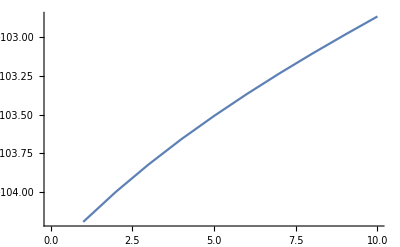

```mathematica
ListLinePlot[trainmllbs[[11-10]]]
```